Got it reasonably cleaned up in DiffGeo4, now I want to do it ALL from scratch, in theory I could put in any coordinates or metric or anything and it would run nicely. Let’s see how it goes.

```mathematica
(*Initial Conditions*)
L0 = 72/(√395);
E0 = √(217/237);
(*L0 = 3.72737;
E0 = 0.95845;*)
r0 = 7.2;
ϕ0 = 0;
t0=0;
θ0=π/2
M0 = 1;
NullOrTimelike = -1
```

π/2

-1

```mathematica
(* Set the dimension and coordinate system *)
d = 4;
coords={t, r, θ, ϕ};
```

```mathematica
(* Define the metric (Schwarzschild here) *)
f[r_]:=1-(2M)/r;
metric={{-f[r],0,0,0},{0,1/f[r],0,0},{0,0,r^2,0},{0,0,0,r^2 Sin[θ]^2}};
inverseMetric=Simplify[Inverse[metric]];
```

```mathematica
(* Define initial velocities for t and ϕ above, then find initial r-velocity from normalisation of the vector. Set null or timelike path above *)
(*u = {ut, ur, uθ, uϕ};*)
u[α_]:=D[coords[[α]][τ],τ];
metricOfτ=metric/.{t->t[τ],r->r[τ],θ->θ[τ],ϕ->ϕ[τ]};
guuEq = Sum[metricOfτ[[a,b]]u[a]u[b], {a, 1, d}, {b, 1, d}];
(*ur0=Simplify[Solve[guuEq==NullOrTimelike, r'[τ]]][[1]]*)
ur0=Simplify[Solve[guuEq==NullOrTimelike, r'[τ]]][[1]]/.{ r[τ]->r0, t[τ]->t0, θ[τ]->θ0, ϕ[τ]->ϕ0, t'[τ]->-E0/f[r0], θ'[τ]->0, ϕ'[τ]->L0/r0^2, r'[τ]->r'[0]}/.M->M0
```

{r'[0]→0.102706+0. ⅈ}

```mathematica
(* Calculate the Christoffel Symbol *)
Γ=Simplify[Table[(1/2)*Sum[(inverseMetric[[i,s]])*
(D[metric[[s,j]],coords[[k]] ]+
D[metric[[s,k]],coords[[j]] ]-D[metric[[j,k]],coords[[s]] ]),{s,1,d}],
{i,1,d},{j,1,d},{k,1,d}] ];
(* Ask Niels if this is a good way to go about it *)
(* Convert the general Christoffel connection to one where the coordinates are functions of time. Really I think this is swapping from the general connection to the connection between different paths or instances of the particle (i.e. we go from r as a coordinate to r_particle(τ) as a component of the position of this object) *)
(* I could also use the metric[τ] I used above but this is cleaner *)
ΓOfτ=Simplify[Table[(1/2)*Sum[(inverseMetric[[i,s]])*
(D[metric[[s,j]],coords[[k]] ]+
D[metric[[s,k]],coords[[j]] ]-D[metric[[j,k]],coords[[s]] ]),{s,1,d}],
{i,1,d},{j,1,d},{k,1,d}] ]/.{t->t[τ], r->r[τ], θ->θ[τ], ϕ->ϕ[τ]};
```

```mathematica
(* Get the geodesic equations for each component *)
timeEq=t''[τ]+Sum[ΓOfτ[[1,μ,ν]]u[μ]u[ν],{μ,1,4},{ν,1,4}];
radialEq=r''[τ]+Sum[ΓOfτ[[2,μ,ν]]u[μ]u[ν],{μ,1,4},{ν,1,4}];
θEq=θ''[τ]+Sum[ΓOfτ[[3,μ,ν]]u[μ]u[ν],{μ,1,4},{ν,1,4}];
ϕEq=ϕ''[τ]+Sum[ΓOfτ[[4,μ,ν]]u[μ]u[ν],{μ,1,4},{ν,1,4}];
```

```mathematica
EqsOfM={timeEq==0, radialEq==0, θEq==0, ϕEq==0,r[0]==r0, r'[0]==(r'[0]/.ur0), ϕ[0]==ϕ0, ϕ'[0]==L/r0^2, t[0]==0, t'[0]==-En/f[r0], θ[0]==Pi/2, θ'[0]==0}
```

{-(2 M r'[τ] t'[τ])/(2 M r[τ]-r[τ]^2)+t''[τ]==0,(M r'[τ]^2)/(2 M r[τ]-r[τ]^2)+(M (-2 M+r[τ]) t'[τ]^2)/r[τ]^3+(2 M-r[τ]) θ'[τ]^2+(2 M-r[τ]) Sin[θ[τ]]^2 ϕ'[τ]^2+r''[τ]==0,(2 r'[τ] θ'[τ])/r[τ]-Cos[θ[τ]] Sin[θ[τ]] ϕ'[τ]^2+θ''[τ]==0,(2 r'[τ] ϕ'[τ])/r[τ]+2 Cot[θ[τ]] θ'[τ] ϕ'[τ]+ϕ''[τ]==0,r[0]==7.2,r'[0]==0.102706+0. ⅈ,ϕ[0]==0,ϕ'[0]==0.0192901 L,t[0]==0,t'[0]==-En/(1-0.277778 M),θ[0]==π/2,θ'[0]==0}

```mathematica
solRange=2000;
eomSol = Block[{M=M0, En=E0, L=L0}, NDSolve[EqsOfM, {r, ϕ}, {τ, 0, solRange}]]
```

{{r→InterpolatingFunction[…],ϕ→InterpolatingFunction[…]}}

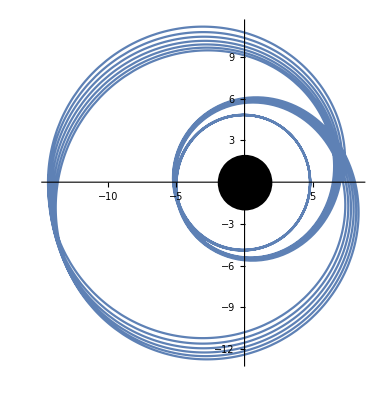

```mathematica
Show[ParametricPlot[Evaluate[{r[τ]Cos[ϕ[τ]],r[τ]Sin[ϕ[τ]]}/.eomSol],{τ,0,solRange}],
Graphics[Disk[{0,0}, 2M0]]]
```

```mathematica
(* Frequency stuff *)
t[χ_, p_, e_]:=p^2 M√(p-2-2e) √(p-2+2e)Integrate[1/(p-2-2e Cos[χprime]) 1/(1+e Cos[χprime])^2 1/(√(p-6-2e Cos[χprime]))/.M->1,{χprime, 0, χ}]
t[2π, 7.6, 0.8]
```

$Aborted

```mathematica
integralSoln=Integrate[1/(p-2-2e Cos[χ]) 1/(1+e Cos[χ])^2 1/(√(p-6-2e Cos[χ]))/.{p->7.6, e->0.8},χ]
```

-(0.142286 √(1.6-1. Cos[χ]) Sin[χ])/(1.25+1. Cos[χ])-(0.0113829 (-1.25-1. Cos[χ]) (5.6-1. Cos[χ]) √(1.+1. Cos[χ]) √(-1.66667+1.66667 Cos[χ]) (15.8982 EllipticPi[-0.15,1. ArcSin[1.29099 √(1.6-1. Cos[χ])],0.230769]-1/(-0.5+1. Cos[χ]^2)9.30745 Cos[2. χ] (1. EllipticF[1. ArcSin[1.29099 √(1.6-1. Cos[χ])],0.230769]-1.12628 EllipticPi[-0.15,1. ArcSin[1.29099 √(1.6-1. Cos[χ])],0.230769]-0.0544244 EllipticPi[0.210526,1. ArcSin[1.29099 √(1.6-1. Cos[χ])],0.230769])+(15.6125 Cos[3. χ] (1. EllipticE[1. ArcSin[1.29099 √(1.6-1. Cos[χ])],0.230769]+1.28846 EllipticF[1. ArcSin[1.29099 √(1.6-1. Cos[χ])],0.230769]-2.40618 EllipticPi[-0.15,1. ArcSin[1.29099 √(1.6-1. Cos[χ])],0.230769]+0.020009 EllipticPi[0.210526,1. ArcSin[1.29099 √(1.6-1. Cos[χ])],0.230769]))/(-7.10543×10^-15+1. Cos[3 χ])-18.5089 EllipticPi[0.210526,1. ArcSin[1.29099 √(1.6-1. Cos[χ])],0.230769]) Sin[χ])/((1.-1. Cos[χ]^2) (-7.-4.35 Cos[χ]+1. Cos[χ]^2))

```mathematica
integralSoln/.χ->π
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression (0.+0. ⅈ) ComplexInfinity encountered.

Indeterminate

```mathematica
Integrate[(p-2-2e Cos[χ] )(1+e Cos[χ])^2 √(p-6-2e Cos[χ])/.{p->6, e->0.5},χ, {χ, 0, 2π}]
```

Integrate::ilim: Invalid integration variable or limit(s) in {χ^2,0,2 π χ}.

∫_0^(2 π χ) (4-1. Cos[χ]) (1+0.5 Cos[χ])^2 √(-1. Cos[χ])ⅆ χ^2

```mathematica
Integrate[Expand[(p-2-2e Cos[χ] )(1+e Cos[χ])^2 √(p-6-2e Cos[χ])/.{p->6, e->0.5}], χ]
```

(√(-1. Cos[χ]) Cos[χ] (4.+3. Cos[χ]-2.22045×10^-16 Cos[χ]^2-0.25 Cos[χ]^3) (-1/(-1.+Tan[0.5 χ]^2)2.66667 √(Cos[χ] Sec[0.5 χ]^4) (0.705357 Hypergeometric2F1[0.25,0.5,1.25,Tan[0.5 χ]^4] Tan[0.5 χ]+1. HypergeometricPFQ[{0.5,0.75},{1.75},Tan[0.5 χ]^4] Tan[0.5 χ]^3)+(8. √(1.-1. Tan[0.5 χ]^4) (1.45238 Tan[0.5 χ]+3.97619 Tan[0.5 χ]^3+3.45238 Tan[0.5 χ]^5+1. Tan[0.5 χ]^7))/(√(Cos[χ] Sec[0.5 χ]^2) (1.+Tan[0.5 χ]^2)^(7/2))))/((2.66667 (Cos[χ] Sec[0.5 χ]^4)^(3/2) Sin[0.5 χ]^2 (0.705357 Hypergeometric2F1[0.25,0.5,1.25,Tan[0.5 χ]^4]+1. HypergeometricPFQ[{0.5,0.75},{1.75},Tan[0.5 χ]^4] Tan[0.5 χ]^2))/(-1.+Tan[0.5 χ]^2)^2-1/(-1.+Tan[0.5 χ]^2)2.66667 √(Cos[χ] Sec[0.5 χ]^4) (-0.5 Sin[χ]+1. Cos[χ] Tan[0.5 χ]) (0.705357 Hypergeometric2F1[0.25,0.5,1.25,Tan[0.5 χ]^4] Tan[0.5 χ]+1. HypergeometricPFQ[{0.5,0.75},{1.75},Tan[0.5 χ]^4] Tan[0.5 χ]^3)-1/(-1.+Tan[0.5 χ]^2)0.940476 Cos[0.5 χ]^2 (Cos[χ] Sec[0.5 χ]^4)^(3/2) (1. Hypergeometric2F1[0.25,0.5,1.25,Tan[0.5 χ]^4]+4.25316 HypergeometricPFQ[{0.5},{},Tan[0.5 χ]^4] Tan[0.5 χ]^2+0.4 Hypergeometric2F1[1.25,1.5,2.25,Tan[0.5 χ]^4] Tan[0.5 χ]^4)+(28. √(Cos[χ] Sec[0.5 χ]^2) √(1.-1. Tan[0.5 χ]^4) (0.207483+1.70408 Tan[0.5 χ]^2+2.46599 Tan[0.5 χ]^4+1. Tan[0.5 χ]^6))/(1.+Tan[0.5 χ]^2)^(7/2)-(8. √(Cos[χ] Sec[0.5 χ]^2) Tan[0.5 χ]^4 (1.45238+3.97619 Tan[0.5 χ]^2+3.45238 Tan[0.5 χ]^4+1. Tan[0.5 χ]^6))/((1.+Tan[0.5 χ]^2)^(7/2) √(1.-1. Tan[0.5 χ]^4))-(28. √(Cos[χ] Sec[0.5 χ]^2) Tan[0.5 χ]^2 √(1.-1. Tan[0.5 χ]^4) (1.45238+3.97619 Tan[0.5 χ]^2+3.45238 Tan[0.5 χ]^4+1. Tan[0.5 χ]^6))/(1.+Tan[0.5 χ]^2)^(9/2)+Sin[χ] (1/(-1.+Tan[0.5 χ]^2)1.33333 √(Cos[χ] Sec[0.5 χ]^4) (0.705357 Hypergeometric2F1[0.25,0.5,1.25,Tan[0.5 χ]^4] Tan[0.5 χ]+1. HypergeometricPFQ[{0.5,0.75},{1.75},Tan[0.5 χ]^4] Tan[0.5 χ]^3)-(4. √(1.-1. Tan[0.5 χ]^4) (1.45238 Tan[0.5 χ]+3.97619 Tan[0.5 χ]^3+3.45238 Tan[0.5 χ]^5+1. Tan[0.5 χ]^7))/(√(Cos[χ] Sec[0.5 χ]^2) (1.+Tan[0.5 χ]^2)^(7/2)))-(4. Cos[χ] √(1.-1. Tan[0.5 χ]^4) (1.45238 Tan[0.5 χ]+3.97619 Tan[0.5 χ]^3+3.45238 Tan[0.5 χ]^5+1. Tan[0.5 χ]^7) (Tan[0.5 χ]-1. Tan[χ]))/(√(Cos[χ] Sec[0.5 χ]^2) (1.+Tan[0.5 χ]^2)^(7/2)))

```mathematica
(* Try using the 2002 paper instead of CKP *)
(* Convert e and p to E and L, which the 2002 paper needs *)

a=0
p=7.6
e=0.8
M=1
En=√(((p-2-2e)(p-2+2e))/(p(p-3-e^2)));
L=√((p^2 M^2)/(p-3-e^2));
x=L-a En;
Vt[χ_]:=a^2 En-(2a M x)/p(1+e Cos[χ])+(En p^2)/(1+e Cos[χ])^2
J[χ_]:=1-(2M)/p(1+e Cos[χ])+a^2/p^2(1+e Cos[χ])^2
Vr[χ_]:=x^2 a^2+2a x En-(2M x^2)/p(3+e Cos[χ])
```

0

7.6

0.8

1

```mathematica
integrand=Vt[χ]/(J[χ]√(Vr[χ]))
integrand
```

(0.+56.5027/(1+0.8 Cos[χ])^2)/((1.-0.263158 M (1+0.8 Cos[χ])) √(0.-0.263158 M (0.+3.81914 √(M^2))^2 (3+0.8 Cos[χ])))

(0.+56.5027/(1+0.8 Cos[χ])^2)/((1.-0.263158 M (1+0.8 Cos[χ])) √(0.-0.263158 M (0.+3.81914 √(M^2))^2 (3+0.8 Cos[χ])))

```mathematica
Integrate[integrand, {χ, 0, 1.9}]
```

∫_0^1.9 (0.+56.5027/(1+0.8 Cos[χ])^2)/((1.-0.263158 (1+0.8 Cos[χ])) √(0.-3.83838 (3+0.8 Cos[χ])))ⅆχ